## [ OLD ]

Preamble

## Package Imports

```mathematica
AppendTo[$Path,"C:\\Users\\deroo\\__DATA\\MEGA\\DATA\\git\\MFDSNT\\Mathematica Notebooks"];
<<BKPNumberTheory`
```

Foreword, etc.

Preliminaries

## Properties of Complex Numbers

### 0.) Preamble

```mathematica
z=1/2+1/2 √3 I;
w=-1/2+1/2 √3 I;
con=3;
w^6//Expand;
```

### 1)

```mathematica
Abs[z];
Abs[w];
Abs[z w];
Abs[z w]===Abs[z]Abs[w]
```

True

### 2)

```mathematica
Abs[w];
Abs[con w];
con Abs[w];
Abs[con w]===con Abs[w]
```

True

### demo)

```mathematica
Abs[ww]"1)"//TraditionalForm
"1)   "  Abs[ww]//TraditionalForm
```

1) Abs[ww]

1)    Abs[ww]

## Triangle Inequality Theorem

```mathematica
Abs[z+w]<=Abs[z]+Abs[w]
```

True

## Reverse Triangle Inequality Theorem

```mathematica
Abs[z+w]<=Abs[z]+Abs[w]
```

True

## Stereographic Projection

(* https://mathematica.stackexchange.com/questions/23793/stereographic-projection *)

Analytic Functions

## Testing Analyticity

```mathematica
FunctionAnalytic[Sqrt[z],z,Complexes]
FunctionAnalytic[{Sqrt[z],Re[z]>0},z,Complexes]
```

False

True

```mathematica
FunctionAnalytic[z^3,z,Complexes]
```

True

```mathematica
FunctionAnalytic[Zeta[z],z,Complexes]
FunctionAnalytic[{Zeta[z],z!=1},z,Complexes]
```

False

True

## Function Visualization

## Cauchy Riemann Equations

[ TBD ]

```mathematica
f[z_]:=z^3-z^2
ComplexExpand[f[z],z]/.{Re[z]:>x,Im[z]:>y}
```

-x^2+x^3+y^2-3 x y^2+ⅈ (-2 x y+3 x^2 y-y^3)

```mathematica
Refine[Re[ComplexExpand[f[z],z]/.{Re[z]:>x,Im[z]:>y}],{Element[x,Reals],Element[y,Reals]}]
Refine[Im[ComplexExpand[f[z],z]/.{Re[z]:>x,Im[z]:>y}],{Element[x,Reals],Element[y,Reals]}]
```

-x^2+x^3+y^2-3 x y^2

-2 x y+3 x^2 y-y^3

```mathematica
D[Refine[Re[ComplexExpand[f[z],z]/.{Re[z]:>x,Im[z]:>y}],{Element[x,Reals],Element[y,Reals]}],x]
D[Refine[Im[ComplexExpand[f[z],z]/.{Re[z]:>x,Im[z]:>y}],{Element[x,Reals],Element[y,Reals]}],y]

D[Refine[Re[ComplexExpand[f[z],z]/.{Re[z]:>x,Im[z]:>y}],{Element[x,Reals],Element[y,Reals]}],y]
-D[Refine[Im[ComplexExpand[f[z],z]/.{Re[z]:>x,Im[z]:>y}],{Element[x,Reals],Element[y,Reals]}],x]
```

-2 x+3 x^2-3 y^2

-2 x+3 x^2-3 y^2

2 y-6 x y

2 y-6 x y

## Length of a path

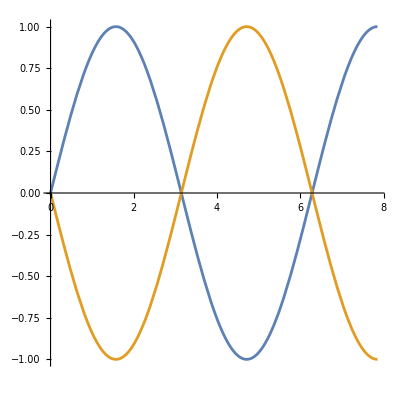

```mathematica
f[x_]:=Sin[x]
Plot[{f[x],Cos[x+Pi/2]},{x,0,2.5Pi},AspectRatio->1]
```

```mathematica
f'[t];
Integrate[√(1+f'[t]^2),{t,0,2Pi}];
Table[Integrate[√(1+Cos'[t-Pi/2]^2),{t,k/2 Pi,2Pi+k/2 Pi}],{k,0,2}]//TableForm
```

4 √2 EllipticE[1/2]
4 √2 EllipticE[1/2]
4 √2 EllipticE[1/2]

Notes

## tmp. notes

```mathematica
ContourIntegrate[z^2,z∈Line[{{0,0},{1,1}}]]
```

-2/3+(2 ⅈ)/3

```mathematica
(1+I)^3/3//Simplify
```

-2/3+(2 ⅈ)/3

```mathematica
ContourIntegrate[z^2,z∈Line[{{0,0},{0,1},{1,0},{1,1}}]]
```

-2/3+(2 ⅈ)/3

```mathematica
CoordinateTransform["Polar"->"Cartesian",{r,θ}]
CoordinateTransform["Cartesian"-> "Polar",{x,y}]
CoordinateTransform["Cartesian"-> "Spherical",{x,y,0}]
```

{r Cos[θ],r Sin[θ]}

{√(x^2+y^2),ArcTan[x,y]}

{√(x^2+y^2),ArcTan[0,√(x^2+y^2)],ArcTan[x,y]}

```mathematica
Conjugate[2+3I]
```

2-3 ⅈ

```mathematica
z=1+2I;
w=-1+√I;
Abs[z]Abs[w]//Simplify
Abs[z w]//Simplify
√3 Abs[z]
Abs[√3 z]
z/Abs[z]//Abs
w/Abs[w]//Abs
```

√(10-5 √2)

√(10-5 √2)

√15

√15

1

1

```mathematica
z/Abs[z]
Abs[z/Abs[z]]
```

(1+2 ⅈ)/(√5)

1

```mathematica
z Conjugate[z]
```

5

```mathematica
Abs[z]
Abs[Conjugate[z]]
```

1

1

```mathematica
ClearAll[w,z]
```

```mathematica
z
```

z

```mathematica
w
```

w

```mathematica
Import["http://www.mathematicaguidebooks.org/V6/downloads/RiemannSurfacePlot3D.m",{"Text","Lines"}];
```

```mathematica
Import["http://www.mathematicaguidebooks.org/V6/downloads/RiemannSurfacePlot3D.m"]
```

```mathematica
rsurf[func_]:=Grid[{{RiemannSurfacePlot3D[w==func,Re[w],{z,w},ImageSize->400,Coloring->Hue[Rescale[ArcTan[1.4 Im[w]],{-Pi/2,Pi/2}]],PlotPoints->{40,40},Boxed->False],RiemannSurfacePlot3D[w==func,Im[w],{z,w},ImageSize->400,Coloring->Hue[Rescale[ArcTan[1.4 Re[w]],{-Pi/2,Pi/2}]],PlotPoints->{40,40},Boxed->False]}}];
```

```mathematica
rsurf[Log[z]]
```

-Graphics3D- | -Graphics3D-

```mathematica
42/5.
```

8.4

```mathematica
ComplexAnalysis`BranchPoints[√(z^2-1),z]
ComplexAnalysis`BranchCuts[√(z^2-1),z]
```

{-1,1,ComplexInfinity}

(-1<Re[z]<0&&Im[z]==0)||Re[z]==0||(0<Re[z]<1&&Im[z]==0)

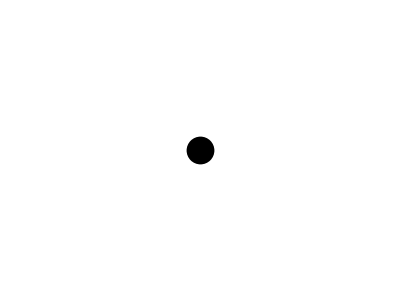
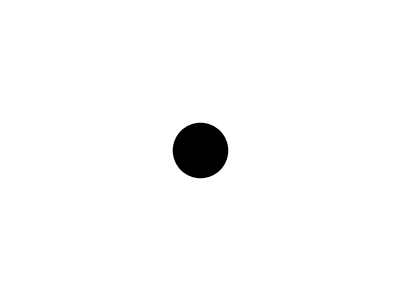
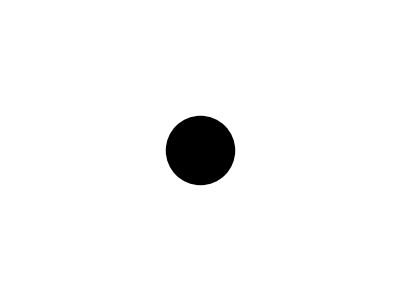
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

{-Graphics-}

```mathematica
Table[Graphics[{PointSize[r],Point[{0,0}]}],{r,{0.02,0.05,0.1,0.3,0.5}}]
Table[Graphics[{AbsolutePointSize[r],Point[{0,0}]}],{r,{4}}]
```

## COMPLEX ANALYSIS

## Ch.

### Par.

#### TOPIC

### Par.

#### TOPIC

```mathematica
2Exp[2/3 Pi I]//ExpToTrig
2Exp[4/3 Pi I]//ExpToTrig
```

-1+ⅈ √3

-1-ⅈ √3

```mathematica
(-1+I √3)^3//Expand
(-1-I √3)^3//Expand
```

8

8

## Visualizing Functions

### Par.

#### TOPIC

### Par.

#### TOPIC

## UZT’s Mathematica

## Color

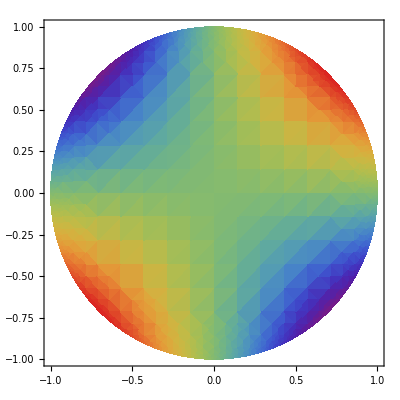

```mathematica
Graphics[DensityPlot[Sin[x y],{x,-1,1},{y,-1,1},
ColorFunction->"Rainbow",
RegionFunction->Function[{x,y,z},x^2+y^2<=1]]
]
```

```mathematica
Graphics[DensityPlot[1,{x,-1,1},{y,-1,1},
ColorFunction->Function[{x,y},RGBColor[x,y,Sqrt[1-x^2-y^2]]],
ColorFunctionScaling->False,
RegionFunction->Function[{x,y,z},x^2+y^2<=1]]
]
```

-Graphics-

```mathematica
Graphics[DensityPlot[1,{x,-1,1},{y,-1,1},
ColorFunction->Function[{x,y},Hue[0.5]],
ColorFunctionScaling->False,
RegionFunction->Function[{x,y,z},x^2+y^2<=1]]
]
```

-Graphics-

```mathematica
Hue[0.5]
```

Hue[0.5]

```mathematica
Table[Apply[RGBColor,ResourceFunction["InverseStereographicProjection"][{m,n}]],{m,0,5,1},{n,0,5,1}]//mf
```

(RGBColor[0, 0, -1] | RGBColor[0, 1, 0] | RGBColor[0, Rational[4, 5], Rational[3, 5]] | RGBColor[0, Rational[3, 5], Rational[4, 5]] | RGBColor[0, Rational[8, 17], Rational[15, 17]] | RGBColor[0, Rational[5, 13], Rational[12, 13]]
RGBColor[1, 0, 0] | RGBColor[Rational[2, 3], Rational[2, 3], Rational[1, 3]] | RGBColor[Rational[1, 3], Rational[2, 3], Rational[2, 3]] | RGBColor[Rational[2, 11], Rational[6, 11], Rational[9, 11]] | RGBColor[Rational[1, 9], Rational[4, 9], Rational[8, 9]] | RGBColor[Rational[2, 27], Rational[10, 27], Rational[25, 27]]
RGBColor[Rational[4, 5], 0, Rational[3, 5]] | RGBColor[Rational[2, 3], Rational[1, 3], Rational[2, 3]] | RGBColor[Rational[4, 9], Rational[4, 9], Rational[7, 9]] | RGBColor[Rational[2, 7], Rational[3, 7], Rational[6, 7]] | RGBColor[Rational[4, 21], Rational[8, 21], Rational[19, 21]] | RGBColor[Rational[2, 15], Rational[1, 3], Rational[14, 15]]
RGBColor[Rational[3, 5], 0, Rational[4, 5]] | RGBColor[Rational[6, 11], Rational[2, 11], Rational[9, 11]] | RGBColor[Rational[3, 7], Rational[2, 7], Rational[6, 7]] | RGBColor[Rational[6, 19], Rational[6, 19], Rational[17, 19]] | RGBColor[Rational[3, 13], Rational[4, 13], Rational[12, 13]] | RGBColor[Rational[6, 35], Rational[2, 7], Rational[33, 35]]
RGBColor[Rational[8, 17], 0, Rational[15, 17]] | RGBColor[Rational[4, 9], Rational[1, 9], Rational[8, 9]] | RGBColor[Rational[8, 21], Rational[4, 21], Rational[19, 21]] | RGBColor[Rational[4, 13], Rational[3, 13], Rational[12, 13]] | RGBColor[Rational[8, 33], Rational[8, 33], Rational[31, 33]] | RGBColor[Rational[4, 21], Rational[5, 21], Rational[20, 21]]
RGBColor[Rational[5, 13], 0, Rational[12, 13]] | RGBColor[Rational[10, 27], Rational[2, 27], Rational[25, 27]] | RGBColor[Rational[1, 3], Rational[2, 15], Rational[14, 15]] | RGBColor[Rational[2, 7], Rational[6, 35], Rational[33, 35]] | RGBColor[Rational[5, 21], Rational[4, 21], Rational[20, 21]] | RGBColor[Rational[10, 51], Rational[10, 51], Rational[49, 51]])

```mathematica
Table[ResourceFunction["InverseStereographicProjection"][{m,n}],{m,0,5,1},{n,0,5,1}]//N //tf
```

0.
0.
-1. | 0.
1.
0. | 0.
0.8
0.6 | 0.
0.6
0.8 | 0.
0.470588
0.882353 | 0.
0.384615
0.923077
1.
0.
0. | 0.666667
0.666667
0.333333 | 0.333333
0.666667
0.666667 | 0.181818
0.545455
0.818182 | 0.111111
0.444444
0.888889 | 0.0740741
0.37037
0.925926
0.8
0.
0.6 | 0.666667
0.333333
0.666667 | 0.444444
0.444444
0.777778 | 0.285714
0.428571
0.857143 | 0.190476
0.380952
0.904762 | 0.133333
0.333333
0.933333
0.6
0.
0.8 | 0.545455
0.181818
0.818182 | 0.428571
0.285714
0.857143 | 0.315789
0.315789
0.894737 | 0.230769
0.307692
0.923077 | 0.171429
0.285714
0.942857
0.470588
0.
0.882353 | 0.444444
0.111111
0.888889 | 0.380952
0.190476
0.904762 | 0.307692
0.230769
0.923077 | 0.242424
0.242424
0.939394 | 0.190476
0.238095
0.952381
0.384615
0.
0.923077 | 0.37037
0.0740741
0.925926 | 0.333333
0.133333
0.933333 | 0.285714
0.171429
0.942857 | 0.238095
0.190476
0.952381 | 0.196078
0.196078
0.960784

```mathematica
ResourceFunction["InverseStereographicProjection"][{4,2}]
ResourceFunction["InverseStereographicProjection"][{4,2}][[1;;2]]
1/2ResourceFunction["InverseStereographicProjection"][{-4,2}][[1;;2]]
1/2 ResourceFunction["InverseStereographicProjection"][{4,2}][[1;;2]]
0.5ResourceFunction["InverseStereographicProjection"][{-4,2}][[1;;2]]
0.5 ResourceFunction["InverseStereographicProjection"][{4,2}][[1;;2]]
0.5ResourceFunction["InverseStereographicProjection"][{-4,2}][[1;;2]]+0.5
0.5 ResourceFunction["InverseStereographicProjection"][{4,2}][[1;;2]]+0.5
Append[0.5ResourceFunction["InverseStereographicProjection"][{-4,2}][[1;;2]]+0.5,1]
Append[0.5 ResourceFunction["InverseStereographicProjection"][{4,2}][[1;;2]]+0.5,1]
Apply[RGBColor,Append[0.5ResourceFunction["InverseStereographicProjection"][{-4,2}][[1;;2]]+0.5,1]]
Apply[RGBColor,Append[0.5 ResourceFunction["InverseStereographicProjection"][{4,2}][[1;;2]]+0.5,1]]
Apply[RGBColor,0.5 ResourceFunction["InverseStereographicProjection"][{-4,-0.5}]+0.5]
Apply[RGBColor,0.5 ResourceFunction["InverseStereographicProjection"][{-10,-3}]+0.5]
```

{8/21,4/21,19/21}

{8/21,4/21}

{-4/21,2/21}

{4/21,2/21}

{-0.190476,0.0952381}

{0.190476,0.0952381}

{0.309524,0.595238}

{0.690476,0.595238}

{0.309524,0.595238,1}

{0.690476,0.595238,1}

RGBColor[0.30952380952380953, 0.5952380952380952, 1]

RGBColor[0.6904761904761905, 0.5952380952380952, 1]

RGBColor[0.2681159420289855, 0.47101449275362317, 0.9420289855072463]

RGBColor[0.40909090909090906, 0.4727272727272727, 0.990909090909091]

```mathematica
RGBColor[0.5,0.5,0.75]
RGBColor[-0.5,0.5,0.75]
RGBColor[-0.5,-0.5,0.75]
RGBColor[0.5,-0.5,0.75]
```

RGBColor[0.5, 0.5, 0.75]

RGBColor[-0.5, 0.5, 0.75]

RGBColor[-0.5, -0.5, 0.75]

RGBColor[0.5, -0.5, 0.75]

```mathematica
Hue[0.5,0.5,0.75]
Hue[-0.5,0.5,0.75]
Hue[-0.5,-0.5,0.75]
Hue[0.5,-0.5,0.75]
```

Hue[0.5, 0.5, 0.75]

Hue[-0.5, 0.5, 0.75]

Hue[-0.5, -0.5, 0.75]

Hue[0.5, -0.5, 0.75]

```mathematica
LABColor[0.5,0.5,0.75]
LABColor[-0.5,0.5,0.75]
LABColor[-0.5,-0.5,0.75]
LABColor[0.5,-0.5,0.75]
```

LABColor[0.5, 0.5, 0.75]

LABColor[-0.5, 0.5, 0.75]

LABColor[-0.5, -0.5, 0.75]

LABColor[0.5, -0.5, 0.75]

```mathematica
ColorData["Gradients"]//tf
```

AlpineColors
Aquamarine
ArmyColors
AtlanticColors
AuroraColors
AvocadoColors
BeachColors
BlueGreenYellow
BrassTones
BrightBands
BrownCyanTones
CandyColors
CherryTones
CMYKColors
CoffeeTones
DarkBands
DarkRainbow
DarkTerrain
DeepSeaColors
FallColors
FruitPunchColors
FuchsiaTones
GrayTones
GrayYellowTones
GreenBrownTerrain
GreenPinkTones
IslandColors
LakeColors
LightTemperatureMap
LightTerrain
MintColors
NeonColors
Pastel
PearlColors
PigeonTones
PlumColors
Rainbow
RedBlueTones
RedGreenSplit
RoseColors
RustTones
SandyTerrain
SiennaTones
SolarColors
SouthwestColors
StarryNightColors
SunsetColors
TemperatureMap
ThermometerColors
ValentineTones
WatermelonColors

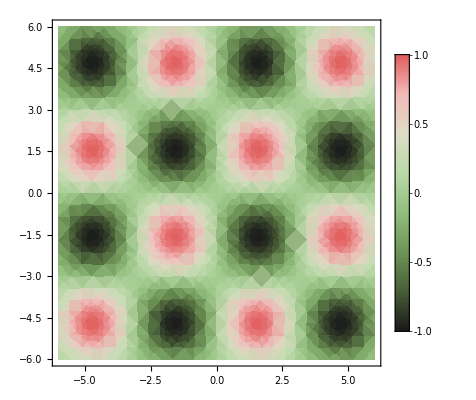

```mathematica
DensityPlot[Sin[x]Sin[y],{x,-6,6},{y,-6,6},ColorFunction->"WatermelonColors",PlotLegends->Automatic]
```

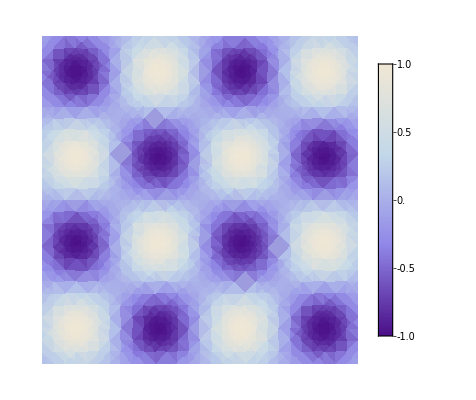

```mathematica
DensityPlot[Sin[x]Sin[y],{x,-6,6},{y,-6,6},ColorFunction->"LakeColors",PlotLegends->Automatic,Frame->None]
```

```mathematica
ComplexPlot[
Cos[3Abs[z]]Sin[Abs[2z]],{z,-2-2I,2+2I},
ColorFunction->Function[{x,y},Hue[(Arg[x+I*y]+Pi)/(2*Pi),Abs[x+I*y]]],
Frame->None
]
```

-Graphics-

```mathematica
Manipulate[
ComplexPlot[
Cos[Abs[a z]]Sin[Abs[b z]],{z,-2-2I,2+2I},
ColorFunction->Function[{x,y},Hue[(Arg[x+I*y]+Pi)/(2*Pi),Abs[x+I*y]]],
Frame->None
],
{a,1,10,0.5},
{b,1,10,0.5},
ControlPlacement->Right
]
```

```mathematica
t:=Table[Subscript[x, i],{i,1,2}]
{{1,0},{0,1}}.t//tf
```

x_1
x_2

```mathematica
Dot[t,t]
```

x_1^2+x_2^2

```mathematica
Manipulate[
ComplexPlot[
Cos[Abs[a z]]Sin[Abs[b z]],{z,-2-2I,2+2I},
ColorFunction->Function[{x,y},Hue[(Arg[x+I*y]+Pi)/(c*Pi),Abs[x+I*y]]],
Frame->None
],
{a,1,10,0.25},
{b,1,10,0.25},
{c,1,10,0.25},
ControlPlacement->Right
]
```

## test

```mathematica
Residue[3/z+2z,{z,0}]
```

3

```mathematica
w
```

√z

```mathematica
ClearAll[w,z]
ResourceFunction["RiemannSurfacePlot3D"][w==Exp[z],Im[z],{w,z}]
```

```mathematica
[w==ⅇ^z,Im[z],{w,z}]
```

[w==ⅇ^z,Im[z],{w,z}]

```mathematica
ResourceFunction["RiemannSurfacePlot3D"][w==z^(1/3),Re[w],{z,w}]
```

-Graphics3D-